### Constants

```mathematica
h = 6.626*10^(-34); (*J s*)
hbar = h/(2π);
e=-1.602*10^(-19); (* C *)
ϵ0=8.854*10^(-12); (* C^2/(J m) *)
me=9.109*10^(-31); (*kg*)
mp=1.673*10^(-27); (*kg*)
μ=(mp/(me+mp))*me;
a0=(4π ϵ0 hbar^2)/(μ e^2);
```

### Bohr hydrogen energies

```mathematica
Ens=Table[-hbar^2/(a0^2 2 μ n^2)*1/(1.602*10^(-19)),{n,1,10}]
```

{-13.5941,-3.39852,-1.51045,-0.84963,-0.543763,-0.377613,-0.27743,-0.212408,-0.167828,-0.135941}

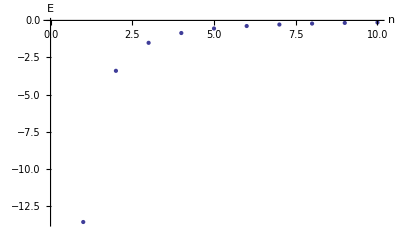

```mathematica
ListPlot[Ens, PlotRange->Full,AxesLabel->{"n", "E"}]
```

### Hydrogen Wave Functions

```mathematica
psi[n_,ρ_]:=Sqrt[(2/(n*a0))^3*((n-1)!)/(2n*(n!)^3)]*ⅇ^-(ρ/ n)*LaguerreL[n-1,1,2*ρ/n]
```

#### test

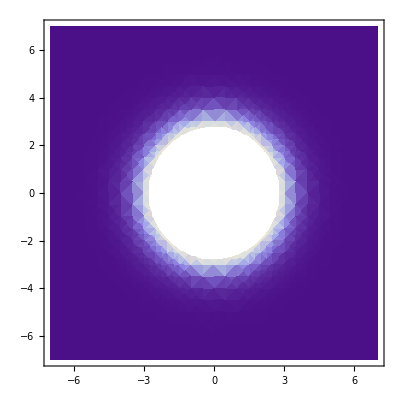
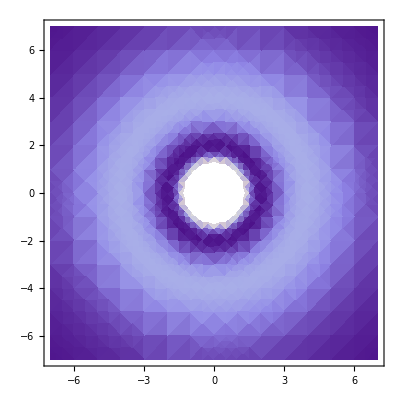
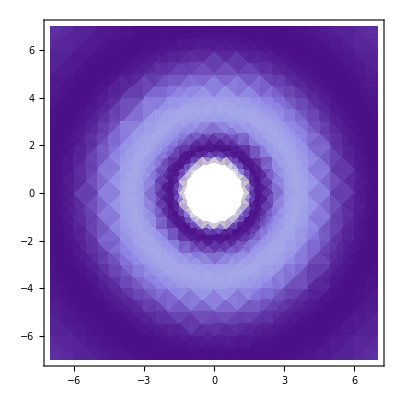
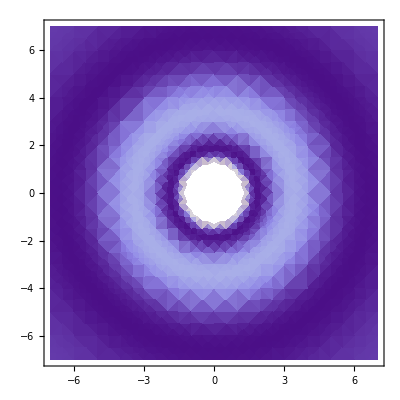
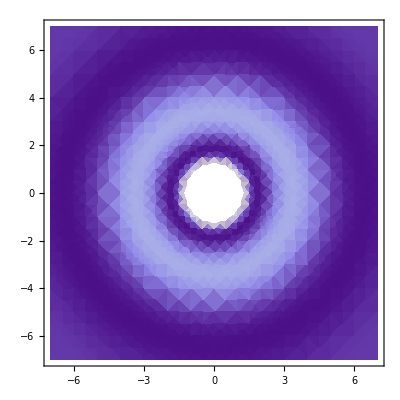
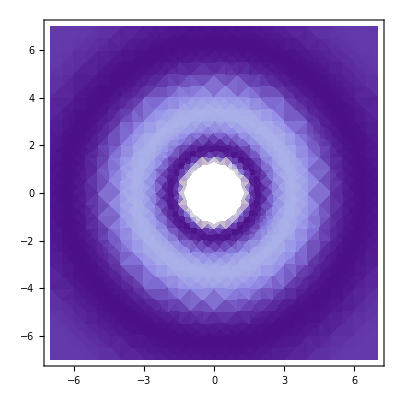

```mathematica
Table[DensityPlot[psi[n,Sqrt[x^2+y^2]]^2,{x,-7,7},{y,-7,7}],{n,1,6}]
```

#### actual file saving part

```mathematica
SetDirectory["~/Desktop/Ellen/Thesis/TeX/Thesis Template/Figures"]
```

/Network/Servers/Knowlton.local/Users/zphantom/Desktop/Ellen/Thesis/TeX/Thesis Template/Figures

```mathematica
Export["densityplots.png",Table[DensityPlot[psi[n,Sqrt[x^2+y^2]]^2,{x,-7,7},{y,-7,7}],{n,1,6}]]
```

densityplots.png

### Hydrogen V_eff

```mathematica
V[r_]:=n^2/2*1/r^2 - 1/r
```

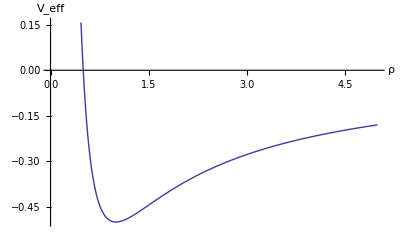

```mathematica
Plot[V[r]/.{n->1},{r,0,5},AxesLabel->{"ρ","V_eff"}]
```

### Yukawa Cutoff

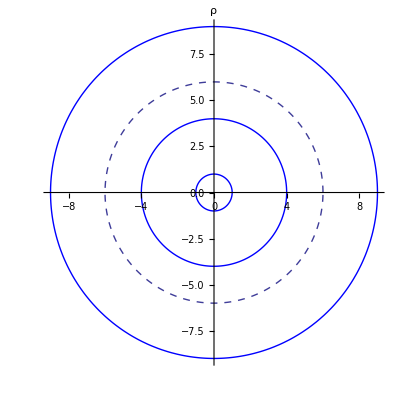

```mathematica
Show[PolarPlot[{1,4,9},{th,0,2π},PlotStyle->Blue,AxesLabel->"ρ"],PolarPlot[6,{th,0,2π},PlotStyle->Dashed]]
```

### Yukawa Veff

```mathematica
V[r_]:=n^2/2*1/r^2 - 1/r*ⅇ^(-r/l)
```

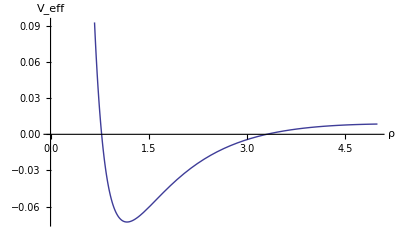

```mathematica
Plot[V[r]/.{n->1,l->1.75},{r,0,5},AxesLabel->{"ρ","V_eff"}]
```